```mathematica
Clear["Global`*"]
```

```mathematica
IntervalRect[{min_,max_}]:=Rectangle[{min,0},{max,1}]
IntervalRect[{min_,max_},kappamax_]:=Rectangle[{min,0},{Min[max,kappamax],1}]
spectrum[list_,max_]:=Graphics[{Black,Thickness[0.0015],Line[{{#,0},{#,1}}]&/@list},PlotRange->{{0,max},{0,1}},PlotRangePadding->None,ImagePadding->{{60,30},{60,0}},ImageSize->Large,AspectRatio->1/10,Axes->None,Frame->{True,False,True,False},FrameLabel->TextCell["Laplace Matrix Eigenvalue",FontSize->14]]
spectrumIntervals[list_,max_,roots_]:=Graphics[{Lighter[Blue,0.85],IntervalRect[#,max]&/@roots,Black,Thickness[0.0015],Line[{{#,0},{#,1}}]&/@list},PlotRange->{{0,max},{0,1}},PlotRangePadding->None,ImagePadding->{{60,30},{60,0}},ImageSize->Large,AspectRatio->1/10,Axes->None,Frame->{True,False,True,False},FrameLabel->TextCell["Laplace Matrix Eigenvalue",FontSize->14]]
InverseParticipationRatio[v_]:=Norm[Normalize[v],4]^4
NormalizeMatrixRows[M_]:=Module[{A=M},
For[i=1,i≤Length[M],++i,
A[[i]]=Normalize[M[[i]],Total]
];
Return[A];
]
```

## Model functions

```mathematica
(*Define functions*)
g[i_,k_]:=x[i,k][t]^phi[[i]];
m[i_,k_]:=x[i,k][t]^mu[[i]];
f[i_,k_]:=t[i,k]x[i,k][t]^psi[[i]](1+Kf[[i]])/(t[i,k]+Kf[[i]]);
t[i_,k_]:=(Sum[A[[i,j]]x[j,k][t],{j,S}])
lo[i_,j_,k_]:=x[i,k][t]^psi[[i]]x[j,k][t](1+Kf[[i]])/(Kf[[i]]+t[i,k])
e[i_,k_]:=-d[[i]]Sum[L[[k,l]]x[i,l][t],{l,Nvertices}]
```

## Import and set parameters

```mathematica
InitParameterZeros[]:=Module[{},
alpha=Table[0,S];

sigma=Table[0,S];
sigmatilde=Table[0,S];
delta=Table[0,S];
deltatilde=Table[0,S];
beta=Table[0,S,S];

psi=Table[0,S];
phi=Table[0,S];
mu=Table[0,S];
gamma=Table[0,S];

M=Table[0,S];
d=Table[0,S];
Kf=Table[0,S];
];

(* Spatial web *)
Nvertices=6;
L={{3,-1,-1,0,0,-1},{-1,3,-1,0,-1,0},{-1,-1,2,0,0,0},{0,0,0,1,0,-1},{0,-1,0,0,1,0},{-1,0,0,-1,0,2}};
```

### 4 Species System

```mathematica
Load4SpeciesParameters[]:=Module[{},
S=4;
index=37;

(*load parameters from file*)
ParLocDyn5=Partition[Import["/home/brechtel/Dokumente/nphys/Data/PAR_4_1_0_0.33.txt","Table"],S+2][[All,2;;-2]];
MA1LocDyn5=Take[Partition[Import["/home/brechtel/Dokumente/nphys/Data/MA1_4_1_0_0.33.txt","Table"],S+1],{1,-1,5+2}][[All,2;;-1]];

(*set parameters*)
InitParameterZeros[];
niche=ParLocDyn5[[index]][[1;;S,2]];
lima=Transpose[MA1LocDyn5[[index]]];

For[i=1,i≤S,++i,
(*body mass*)
M[[i]]=10^(4niche[[i]]);

(*migration rate*)
d[[i]]=2. 10^-2 M[[i]]^-1;

(*biomass flow*)
alpha[[i]]=ParLocDyn5[[index]][[i,-1]];

(*exponent parameters*)
psi[[i]]=ParLocDyn5[[index]][[i,14]];
phi[[i]]=ParLocDyn5[[index]][[i,13]];
mu[[i]]=ParLocDyn5[[index]][[i,18]];
gamma[[i]]=ParLocDyn5[[index]][[i,16]];
Kf[[i]]=gamma[[i]]/(1-gamma[[i]]);

(*scale parameters*)
sigma[[i]]:=Sum[lima[[n,i]],{n,S}]/(Sum[lima[[n,i]],{n,S}]+1);
sigmatilde[[i]]=1-sigma[[i]];

If[Sum[lima[[i,j]],{j,S}]>0,delta[[i]]=1,delta[[i]]=0];
deltatilde[[i]]=1-delta[[i]];

For[j=1,j≤S,++j,beta[[j,i]]=If[sigma[[i]]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0]];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=3;
];
```

(0. | 0.454909 | 0. | 0.545091
0. | 0. | 0. | 1.
0. | 1. | 0. | 0.
0. | 0. | 0. | 0.)

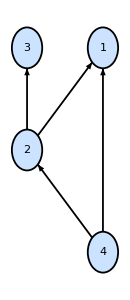

```mathematica
Load4SpeciesParameters[]
MatrixForm[A]
plt5s=GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->{130,300}
]
```

### 5 Species System (oscillation)

```mathematica
Load5SpeciesParameters[]:=Module[{},
S=5;
index=1;

(*load parameters from file*)
ParLocDyn5=Partition[Import["/home/brechtel/Dokumente/nphys/Data/Oszillation/PAR.txt","Table"],S+2][[All,2;;-2]];

MA1LocDyn5=Take[Partition[Import["/home/brechtel/Dokumente/nphys/Data/Oszillation/MA.txt","Table"],S+1],{1,-1,5+2}][[All,2;;-1]];

(*set parameters*)
InitParameterZeros[];
niche=ParLocDyn5[[index]][[1;;S,2]];
lima=Transpose[MA1LocDyn5[[index]]];

For[i=1,i≤S,++i,
(*body mass*)
M[[i]]=10^(8niche[[i]]);

(*migration rate*)
d[[i]]=10^1  M[[i]]^-1;

(*biomass flow*)
alpha[[i]]=ParLocDyn5[[index]][[i,-1]];

(*exponent parameters*)
psi[[i]]=ParLocDyn5[[index]][[i,14]];
phi[[i]]=ParLocDyn5[[index]][[i,13]];
mu[[i]]=ParLocDyn5[[index]][[i,18]];
gamma[[i]]=ParLocDyn5[[index]][[i,16]];
Kf[[i]]=gamma[[i]]/(1-gamma[[i]]);

(*scale parameters*)
sigma[[i]]=Sum[lima[[n,i]],{n,S}]/(Sum[lima[[n,i]],{n,S}]+1);
sigmatilde[[i]]=1-sigma[[i]];

If[Sum[lima[[i,j]],{j,S}]>0,delta[[i]]=1,delta[[i]]=0];
deltatilde[[i]]=1-delta[[i]];

For[j=1,j≤S,++j,beta[[j,i]]=If[sigma[[i]]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0]];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=3;
];
```

(0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 0.)

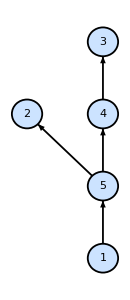

```mathematica
Load5SpeciesParameters[]
MatrixForm[A]
plt5s=GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->{130,300}
]
```

```mathematica
(*Export["5SpeciesWebOscillation.svg",plt5s];*)
```

## Model Equations

```mathematica
(* Homogeneous system equations right hand side *)
rhs[i_,k_]:=alpha[[i]](deltatilde[[i]]g[i,k]
+delta[[i]]If[Sum[lima[[i,j]],{j,S}]>0,f[i,k],0]
-sigmatilde[[i]]m[i,k]
-sigma[[i]]Sum[beta[[j,i]]If[beta[[j,i]]>0,lo[j,i,k],0],{j,S}])
```

```mathematica
Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]]
```

{x[1,1]'[t]==0.82439 ((x[1,1][t])^0.5-0.487575 (x[1,1][t])^1.-0.512425 (0.+(4. x[1,1][t] (x[5,1][t])^1.)/(3.+1. x[1,1][t]))),x[2,1]'[t]==0.018593 (0.-1. (x[2,1][t])^1.+(4. (x[2,1][t])^1. (0.+1. x[5,1][t]))/(3.+1. x[5,1][t])),x[3,1]'[t]==0.01045 (0.-1. (x[3,1][t])^1.+(4. (x[3,1][t])^1. (0.+1. x[4,1][t]))/(3.+1. x[4,1][t])),x[4,1]'[t]==0.059253 (-0.504902 (x[4,1][t])^1.-0.495098 (0.+(4. (x[3,1][t])^1. x[4,1][t])/(3.+1. x[4,1][t]))+(4. (x[4,1][t])^1. (0.+1. x[5,1][t]))/(3.+1. x[5,1][t])),x[5,1]'[t]==0.305557 (-0.331963 (x[5,1][t])^1.+(4. (0.+1. x[1,1][t]) (x[5,1][t])^1.)/(3.+1. x[1,1][t])-0.668037 (0.+(1.82697 (x[2,1][t])^1. x[5,1][t])/(3.+1. x[5,1][t])+(2.17303 (x[4,1][t])^1. x[5,1][t])/(3.+1. x[5,1][t])))}

## Local Web

### Niche Web

```mathematica
SetFoodWebNiche[]:=Module[{},

GenerateFoodWeb[S_]:=Module[
{connectance=0.25,beta,r,c,A=Table[0,{S},{S}],foodweb,i,j},
While[True,
connectance=0.25;
beta=(1-2connectance)/(2connectance);

niche=Sort[Table[RandomReal[],{S+1}]];
r=Table[RandomVariate[BetaDistribution[1,beta]],{S}];
c=Table[RandomReal[{niche[[i]]r[[i]]/2,niche[[i]]}],{i,S}];

For[i=1,i≤S,++i,
For[j=1,j<i,++j,
If[c[[i]]-niche[[i]]r[[i]]/2<niche[[j]]<c[[i]]+niche[[i]]r[[i]]/2,A[[i,j]]=1,A[[i,j]]=0];
];
];
foodweb=AdjacencyGraph[A];
If[WeaklyConnectedGraphQ[foodweb],Break[]];
];
lima=NormalizeMatrixRows[A];
Return[foodweb];
];

];

NormalizeMatrixRows[M_]:=Module[{A=M},
For[i=1,i≤Length[M],++i,
A[[i]]=Normalize[M[[i]],Total];
];
Return[A];
]

calcNumberOfPrey[i_]:=Module[{j,n=0},
For[j=1,j≤i,++j,
If[lima[[i,j]]>0,++n];
];
Return[n];
];
```

### Niche Web Normal Distribution

```mathematica
SetFoodWebNicheNormal[]:=Module[{},

GenerateFoodWeb[S_]:=Module[
{connectance=0.25,beta,r,c,A=Table[0,{S},{S}],Lima=Table[0,{S},{S}],foodweb,i,j},
While[True,
connectance=0.25;
beta=(1-2connectance)/(2connectance);

niche=Sort[Table[RandomReal[],{S+1}]];
r=Table[RandomVariate[BetaDistribution[1,beta]],{S}];
c=Table[RandomReal[{niche[[i]]r[[i]]/2,niche[[i]]}],{i,S}];

For[i=1,i≤S,++i,
For[j=1,j<i,++j,
If[c[[i]]-niche[[i]]r[[i]]/2<niche[[j]]<c[[i]]+niche[[i]]r[[i]]/2,
A[[i,j]]=1;
Lima[[i,j]]=Abs[RandomVariate[NormalDistribution[]]];
,
A[[i,j]]=0;
Lima[[i,j]]=0];
];
];
foodweb=AdjacencyGraph[A];
If[WeaklyConnectedGraphQ[foodweb],Break[]];
];
lima=NormalizeMatrixRows[Lima];
Return[foodweb];
];

];
```

## Parameters

### Parameters

```mathematica
calcParameters[S_]:=Module[{},
calcScaleParameters[S];
calcExponentParameters[S];
];
```

```mathematica
calcScaleParameters[S_]:=Module[{},
(* local foodweb *)
beta=Table[calcBeta[i,j],{i,S},{j,S}];

sigma=Table[calcSigma[i],{i,S}];
sigmatilde=Table[calcSigmatilde[i],{i,S}];

chi=Table[calcChi[i,j],{i,S},{j,S}];
delta=Table[calcDelta[i],{i,S}];
deltatilde=Table[calcDeltatilde[i],{i,S}];

rho=Table[calcRho[i],{i,S}];
rhotilde=Table[calcRhotilde[i],{i,S}];

alphaP=Table[calcAlphaP[i],{i,S}];
alphaC=Table[calcAlphaC[i],{i,S}];
];
```

#### Exponent

```mathematica
calcExponentParameters[S_]:=Module[{i,j},
(* local foodweb *)
gamma=calcGamma[];
lambda=calcLambda[];
phi=calcPhi[];
psi=calcPsi[];
mu=calcMu[];

(* migration *)
omega=calcOmega[];
omegahat=calcOmegahat[];

kappa=calcKappa[];
kappahat=calcKappahat[];
];
```

```mathematica
SetExponentParameterCalculationHolling2[]:=Module[{},
(* local foodweb *)
calcGamma[]:=Table[RandomReal[],{i,S}];
calcLambda[]:=Table[If[lima[[i,j]]>0,RandomReal[{1,2}],0],{i,S},{j,S}];
calcPhi[]:=Table[1,{i,S}];
calcPsi[]:=Table[1,{i,S}];
calcMu[]:=Table[RandomReal[{1,2}],{i,S}];

(* migration *)
calcOmega[]:=Table[RandomReal[{0,1}],{i,S}];
calcOmegahat[]:=Table[RandomReal[{0,1}],{i,S}];
calcKappa[]:=Table[0,{i,S},{j,S}];
calcKappahat[]:=Table[0,{i,S},{j,S}];
];
```

```mathematica
SetExponentParameterCalculationHolling3[]:=Module[{},
(* local foodweb *)
calcGamma[]:=Table[RandomReal[{0,2}],{i,S}];
calcLambda[]:=Table[If[lima[[i,j]]>0,RandomReal[{1,2}],0],{i,S},{j,S}];
calcPhi[]:=Table[1,{i,S}];
calcPsi[]:=Table[1,{i,S}];
calcMu[]:=Table[RandomReal[{1,2}],{i,S}];

(* migration *)
calcOmega[]:=Table[RandomReal[{0,1}],{i,S}];
calcOmegahat[]:=Table[RandomReal[{0,1}],{i,S}];

calcKappa[]:=Table[0,{i,S},{j,S}];
calcKappahat[]:=Table[0,{i,S},{j,S}];
];
```

```mathematica
SetExponentParameterCalculationStandart[]:=Module[{},
(* local foodweb *)
calcGamma[]:=Table[RandomReal[{0,2}],{i,S}];
calcLambda[]:=Table[If[lima[[i,j]]>0,RandomReal[{1,2}],0],{i,S},{j,S}];
calcPhi[]:=Table[RandomReal[],{i,S}];
calcPsi[]:=Table[RandomReal[],{i,S}];
calcMu[]:=Table[RandomReal[{1,2}],{i,S}];

(* migration *)
calcOmega[]:=Table[RandomReal[{-2,2}],{i,S}];
calcOmegahat[]:=Table[RandomReal[{-2,2}],{i,S}];

calcKappa[]:=Table[RandomReal[{-2,2}],{i,S},{j,S}];
calcKappahat[]:=Table[RandomReal[{-2,2}],{i,S},{j,S}];
];
```

```mathematica
SetExponentParameterCalculationAdaptive[]:=Module[{},
(* local foodweb *)
calcGamma[]:=Table[RandomReal[{0,2}],{i,S}];
calcLambda[]:=Table[If[lima[[i,j]]>0,RandomReal[{1,2}],0],{i,S},{j,S}];
calcPhi[]:=Table[RandomReal[],{i,S}];
calcPsi[]:=Table[RandomReal[],{i,S}];
calcMu[]:=Table[RandomReal[{1,2}],{i,S}];

(* migration *)
calcOmega[]:=Table[RandomReal[{0,1}],{i,S}];
calcOmegahat[]:=Table[RandomReal[{0,1}],{i,S}];

calcKappa[]:=Table[If[lima[[j,i]]>0,RandomReal[],0],{i,S},{j,S}];
calcKappahat[]:=Table[If[lima[[i,j]]>0,RandomReal[],0],{i,S},{j,S}];
];
```

### Local

```mathematica
SetScaleParameterCalculation[]:=Module[{},
(* biomass flow *)
calcAlphaP[i_]:=rhotilde[[i]]10^(-2niche[[i]]);
calcAlphaC[i_]:=rho[[i]]10^(-2niche[[i]]);

calcRho[i_]:=RandomReal[{0,1}];
calcRhotilde[i_]:=1-rho[[i]];

(* loss by local predation and respiration *)
calcSigma[i_]:=If[Sum[lima[[j,i]],{j,S}]>0,RandomReal[{0,1}],0];
calcSigmatilde[i_]:=1-sigma[[i]];
calcBeta[i_,j_]:=If[Sum[lima[[n,j]],{n,S}]>0,lima[[i,j]]/Sum[lima[[n,j]],{n,S}],0];

(* gain by predation *)
calcDelta[i_]:=If[Sum[lima[[i,j]],{j,S}]>0,1,0];
calcDeltatilde[i_]:=1-delta[[i]];
calcChi[i_,j_]:=If[lima[[i,j]]>0,lima[[i,j]]/Sum[lima[[i,n]],{n,S}],0];

(* feeding links *)
input[i_,j_]:=alphaP[[i]]delta[[i]]chi[[i,j]];
output[i_,j_]:=alphaP[[j]]sigma[[j]]beta[[i,j]];
];
```

## Jacobian

```mathematica
calcP[i_,j_]:=If[i==j,
alphaP[[i]](deltatilde[[i]] phi[[i]]+delta[[i]] psi[[i]]- sigmatilde[[i]] mu[[i]]-sigma[[i]] Sum[beta[[n,i]]lambda[[n,i]]((gamma[[n]]-1)chi[[n,i]]+1),{n,S}]),
alphaP[[i]](delta[[i]] gamma[[i]] chi[[i,j]]lambda[[i,j]] -sigma[[i]]( beta[[j,i]]psi[[j]]+Sum[beta[[n,i]]lambda[[n,j]](gamma[[n]]-1)chi[[n,j]],{n,S}]))
];
```

```mathematica
calcC[i_,j_]:=If[i==j,
alphaC[[i]](omegahat[[i]]-omega[[i]]),
alphaC[[i]](kappahat[[i,j]]-kappa[[i,j]])
];
```

```mathematica
calcJ[Np_,L_]:=
ArrayFlatten[
Table[
If[k==l,
JP+L[[k,l]]JC,
L[[k,l]]JC],
{k,Np},{l,Np}]
];
```

```mathematica
initParameters[S_]:=Module[{},
omega=Table[ToExpression["omega"<>ToString[i]],{i,S}];
omegahat=Table[ToExpression["omegahat"<>ToString[i]],{i,S}];
kappa=Table[ToExpression["kappa"<>ToString[i]],{i,S}];
kappahat=Table[ToExpression["kappahat"<>ToString[i]],{i,S}];
];
```

```mathematica
calcMatrices[S_]:=Module[{},
JP=Table[calcP[i,j],{i,S},{j,S}];
JC=Table[calcC[i,j],{i,S},{j,S}];
];
```

```mathematica
(* Jacobi Matrix *)

NonDiagonalMatrix[Np_]:=Table[1,{Np},{Np}]-IdentityMatrix[Np];

OnesRow[Np_]:={Table[1,{Np}]};
OnesColumn[Np_]:=Transpose[OnesRow[Np]];

calcJacobian[S_,Np_,L_]:=Module[{n=Np+1,k,l,J,ND},
calcMatrices[S];
J=calcJ[Np,L];
Return[J];
];
```

## Jacobian

```mathematica
CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
JP=FullSimplify[J/.Table[x[i,1][t]->1,{i,S}]];
JC=DiagonalMatrix[Table[d[[i]],{i,S}]];
];

CalculateMSF[]:=Module[{points,dkappa=0.1},
If[!ValueQ[kappamax],kappamax=15];
CalculateJacobian[];
points=Table[{kappa,Max[Re[Eigenvalues[JP-kappa JC]]]},{kappa,-10,kappamax,dkappa}];
MSF=Interpolation[points,InterpolationOrder->1];
Return[MSF]
];

CalculateReCoMSF[]:=Module[{points,dkappa=0.01,kappa},
If[!ValueQ[kappamax],kappamax=15];
CalculateJacobian[];

RePoints={};
CoPoints={};

For[kappa=-1,kappa≤kappamax,kappa+=dkappa,
EV=First[MaximalBy[ReIm[Eigenvalues[JP-kappa JC]],First]];
If[Abs[EV[[2]]]==0,
AppendTo[RePoints,{kappa,EV[[1]]}];
,
AppendTo[CoPoints,{kappa,EV[[1]]}];
];
];
];

CalculateReCoMSF[JP_,JC_]:=Module[{points,dkappa=0.01,kappa},
If[!ValueQ[kappamax],kappamax=15];
CalculateJacobian[];

RePoints={};
CoPoints={};

For[kappa=-1,kappa≤kappamax,kappa+=dkappa,
EV=First[MaximalBy[ReIm[Eigenvalues[JP-kappa JC]],First]];
If[Abs[EV[[2]]]==0,
AppendTo[RePoints,{kappa,EV[[1]]}];
,
AppendTo[CoPoints,{kappa,EV[[1]]}];
];
];
];

PlotCoReMSF[RePoints_,CoPoints_]:=Module[{},
Return[
ListPlot[
{RePoints,CoPoints},
Frame->True,
FrameLabel->{"Laplacian eigenvalue κ","Max Re Jacobian eigenvalue"},
Joined->True,
PlotRange->{{0,kappamax},Automatic}
]
];
]

PlotCoReMSF[RePoints_,CoPoints_,plotRange_]:=Module[{},
Return[
ListPlot[
{RePoints,CoPoints},
Frame->True,
FrameLabel->{"Laplacian eigenvalue κ","Max Re Jacobian eigenvalue"},
Joined->True,
PlotRange->plotRange
]
];
]

(*Find unstable interval*)
FindUnstableInterval[MSF_]:=Module[{kappa0,kappa,step=0.001,roots},
intervals={};
roots={};
If[!ValueQ[kappamax],kappamax=15];

For[kappa=0,kappa+step≤kappamax,kappa+=step,
If[MSF[kappa]MSF[kappa+step]<0,AppendTo[roots,kappa+step/2]];
];

If[Length[roots]==0,
Print["Failed to find unstable interval."];
Abort[];
];

For[i=1,i≤Length[roots],i+=2,
If[i+1≤Length[roots],
AppendTo[intervals,{roots[[i]],roots[[i+1]]}],
Print["Failed to find maximum of the last unstable interval. Set maximum to kappamax."];
AppendTo[intervals,{roots[[i]],kappamax}];
];
];

interval=First[intervals];
];
```

Failed to find maximum of the last unstable interval. Set maximum to kappamax.

{{0.1855,0.9135},{9.6955,15}}

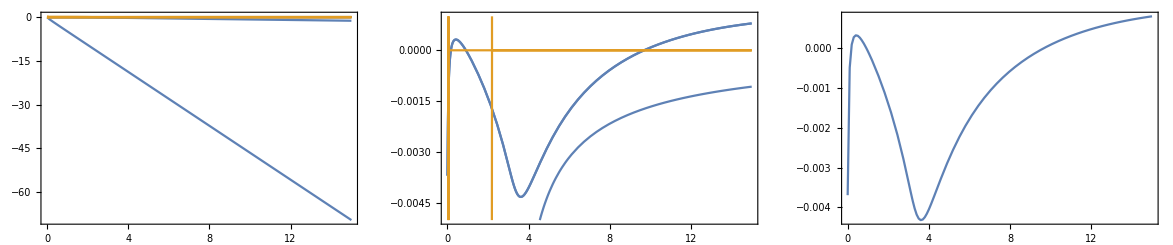

```mathematica
CalculateJacobian[];
MSF=CalculateMSF[];
FindUnstableInterval[MSF];
intervals

GraphicsRow[{
Plot[{Sort[Re[Eigenvalues[JP-kappa JC]]],Sort[Im[Eigenvalues[JP-kappa JC]]]},{kappa,0,kappamax},PlotRange->Full,Frame->True,ImageSize->Medium],
Plot[{Sort[Re[Eigenvalues[JP-kappa JC]]],Sort[Im[Eigenvalues[JP-kappa JC]]]},{kappa,0,kappamax},PlotRange->{-0.005,0.001},Frame->True,ImageSize->Medium],
Plot[MSF[kappa],{kappa,0,kappamax},Frame->True,ImageSize->Medium]
}]

If[ValueQ[kappaList],spectrumIntervals[kappaList,kappamax,intervals]]
```

```mathematica
kappa=0;
ReIm[Eigenvalues[JP-kappa JM]]
MaximalBy[ReIm[Eigenvalues[JP-kappa JM]],First]
```

{{-0.116059,0.261433},{-0.116059,-0.261433},{-0.00369157,0.0107155},{-0.00369157,-0.0107155},{-0.00872022,0.}}

{{-0.00369157,0.0107155},{-0.00369157,-0.0107155}}

0.5

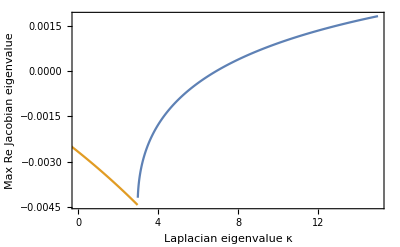

```mathematica
Load4SpeciesParameters[];
phi[[4]]=0.5
CalculateReCoMSF[];
MSFPlot1=PlotCoReMSF[RePoints,CoPoints]
```

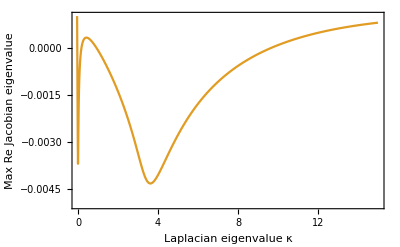

```mathematica
Load5SpeciesParameters[];
CalculateReCoMSF[];
MSFPLot2=PlotCoReMSF[RePoints,CoPoints,{{0,kappamax},{-0.005,0.001}}]
```

```mathematica
Export["MSF4S.pdf",MSFPlot1]
Export["MSF5S.pdf",MSFPLot2]
```

MSF4S.pdf

MSF5S.pdf

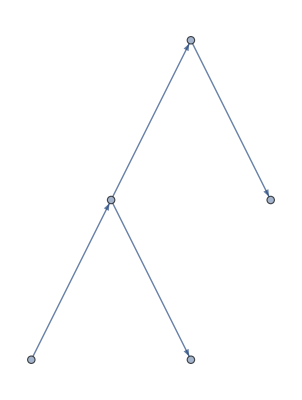

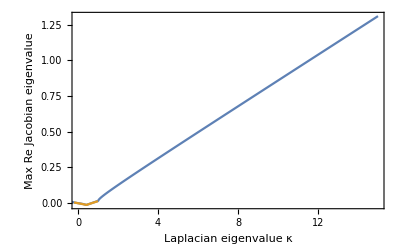

```mathematica
SetFoodWebNicheNormal[];
SetScaleParameterCalculation[];
SetExponentParameterCalculationStandart[];
GenerateFoodWeb[S]
calcParameters[S]
calcMatrices[S]
CalculateReCoMSF[JP,JC]
PlotCoReMSF[RePoints,CoPoints]
```

## Spatial Web

```mathematica
FindSpacialWeb[nvertices_,r_,n_]:=Module[{maxtries,tries},
Nvertices=nvertices;
R=r;

maxtries=1000;
tries=0;
While[tries<maxtries,
++tries;
graph=RandomGraph[SpatialGraphDistribution[Nvertices,R/Sqrt[Nvertices]]];
If[!ConnectedGraphQ[graph],Continue[]];
L=KirchhoffMatrix[graph];
kappaList=N[Eigenvalues[L]];
If[ValueQ[intervals],
If[Count[kappaList,x_/;Apply[Or,Table[intervals[[i,1]]<x<intervals[[i,2]],{i,Length[intervals]}]]]==n,
If[n>0,unstable=Position[kappaList,x_/;Apply[Or,Table[intervals[[i,1]]<x<intervals[[i,2]],{i,Length[intervals]}]]][[1,1]];
];
Break[]],
Break[]]
];
If[tries==maxtries,Print["No matching spatial web found after "<>ToString[maxtries]" tries."],Print["Matching spatial web found after "<>ToString[tries]" tries."]];
vlist=N[Eigenvectors[L]];
If[!ValueQ[unstable],unstable=1];
If[!ValueQ[kappamax],kappamax=Ceiling[Max[kappaList],5]];
];

FindUnstableSpatialWeb[Nvertices_,R_]:=FindSpacialWeb[Nvertices,R,1];
FindStableSpatialWeb[Nvertices_,R_]:=FindSpacialWeb[Nvertices,R,0];

ShowSpatialWeb[]:=Module[{},
Print[graph];
If[ValueQ[intervals],
Print[spectrumIntervals[Eigenvalues[L],kappamax,intervals]],
Print[spectrum[Eigenvalues[L],kappamax]]
]
];
```

Failed to find maximum of the last unstable interval. Set maximum to kappamax.

Matching spatial web found after 43  tries.

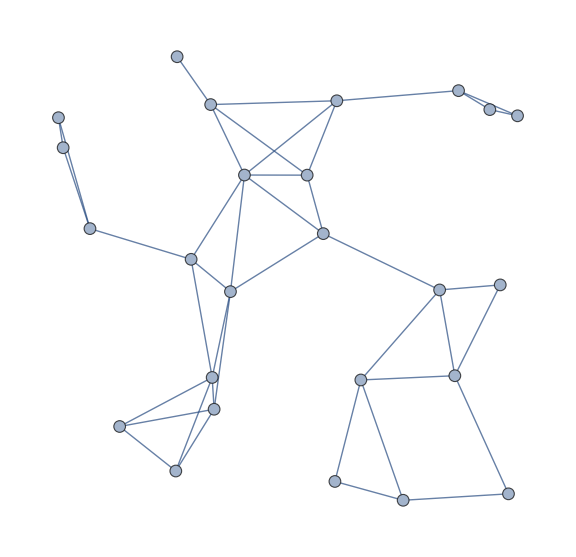

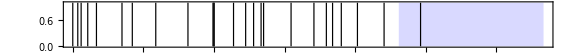

```mathematica
Load4SpeciesParameters[];
MSF=CalculateMSF[];
FindUnstableInterval[MSF];

Clear[kappamax];
FindSpacialWeb[25,1.3,1];
ShowSpatialWeb[];
```

Failed to find maximum of the last unstable interval. Set maximum to kappamax.

Matching spatial web found after 3  tries.

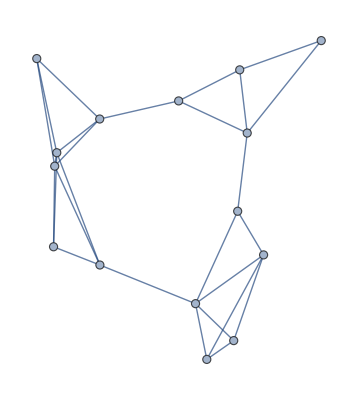

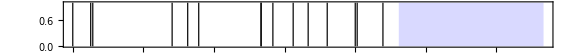

```mathematica
Load4SpeciesParameters[];
MSF=CalculateMSF[];
FindUnstableInterval[MSF];

Clear[kappamax];
FindSpacialWeb[15,1.3,0];
ShowSpatialWeb[];
```

```mathematica
(* Stable for 4 species system *)
LoadSpatialWeb[]:=Module[{},
L={{4,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,-1},{0,3,0,-1,-1,0,0,0,0,-1,0,0,0,0,0},{0,0,2,0,0,0,0,-1,0,0,-1,0,0,0,0},{0,-1,0,3,-1,0,0,0,0,0,-1,0,0,0,0},{0,-1,0,-1,3,-1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,-1,4,0,0,0,0,0,0,-1,0,-1},{-1,0,0,0,0,0,3,0,0,0,0,-1,0,0,-1},{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,3,0,-1,0,-1,-1,0},{0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,-1,-1,0,0,0,0,-1,0,5,0,-1,-1,0},{-1,0,0,0,0,0,-1,0,0,0,0,3,0,0,-1},{0,0,0,0,0,-1,0,0,-1,0,-1,0,4,-1,0},{0,0,0,0,0,0,0,0,-1,0,-1,0,-1,3,0},{-1,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,4}}
];
```

## Homogeneous System

```mathematica
(*set starting conditions*)
setStartHomogen[]:=Module[{delta=0.01},
startHomogen=
Flatten[
Table[
x[i,k][0]==RandomReal[{1-delta,1+delta}],
{i,S},{k,1}]
];
];

(*Solve ODE*)
solveHomogen[Tmax_]:=Module[{sol},
setStartHomogen[];
sol=NDSolve[Join[{eqnsHomogen,startHomogen}],varsHomogen,{t,0,Tmax},MaxSteps->100000][[1]];
Return[varsHomogen/.sol];
];

EvaluateHomogenSystem[Tmax_]:=Module[{},
(*generate equations*)
eqnsHomogen=Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]];

(*dependent variables*)
varsHomogen = Flatten[
Table[
x[i,k][t]
,{i,S},{k,1}]
];

(*solve deqns*)
solHomogen=solveHomogen[Tmax];
XSList=solHomogen/.t->Tmax;

(*set steady state values*)
For[i=1,i≤S,++i,
XS[i]=XSList[[i]];
(*TS[i]=Sum[c[[i,j]]XS[j],{j,S}];*)
];
];
```

## Solver

### Local

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocal[]:=Module[{y},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.01,0.01}];
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocal[noise_,tmax_,maxSteps_]:=Module[{y},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1;
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaLocal[noise_]:=Module[{y},
EulerMaruyamaLocal[noise,100,100000];
];
```

### Spatial

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatial[Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.01,0.01}];
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1;
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

```mathematica
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_,initialData_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

### Local variable phi

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocalVariable[Interval_]:=Module[{y,phistep,phit,step},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.01,0.01}];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocalVariable[Interval_,noise_,tmax_,maxSteps_]:=Module[{y,phistep,phit,step},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.01,0.01}];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaLocalVariable[Interval_,noise_]:=Module[{y},
EulerMaruyamaLocalVariable[Interval,noise,100,100000];
];
```

### Spatial variable phi

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatialVariable[Interval_]:=Module[{y,phistep,phit,step},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.01,0.01}];
];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatialVariable[Interval_,noise_,tmax_,maxSteps_]:=Module[{y,phistep,phit},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1;
];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaSpatialVariable[Interval_,noise_]:=Module[{y},
EulerMaruyamaSpatialVariable[Interval,noise,100,100000];
];

EulerMaruyamaSpatialVariable[Interval_,noise_,tmax_,maxSteps_,initialData_]:=Module[{y,phit,phistep},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```